```mathematica
(* This code evaluates the integral over phi in the entangled cat states generated from a number state. *)
(* Notes of 7/2/19. *)

(* First do the state from the beam splitter, which gives part of the results for phi++ and phi__. *)

Clear[x1,x2,phi,n,r];

(* Choose values of variables. *)

(* Number of photons in the initial Fock state. *)
n=24;

(* Arbitrary choice of the parameter r. *)
r=Sqrt[n];

(* Width - standard deviation of the gaussian for wave function. *)
(* Squaring will give half that for probability density. *)
w=2;




(* First calculate the state immediately after the beam splitter. *)
(*  This is the same as phi++  plus  phi--, aside from the cosine^2 factor. *)


(* Calculate the wave function. *)

psi[x1_,x2_]:=NIntegrate[Exp[-I*n*phi]*Exp[I*r/Sqrt[2]*Sin[phi]*x1]*Exp[I*r/Sqrt[2]*Sin[phi]*x2]*Exp[-(x1-r/Sqrt[2]*Cos[phi])^2/(2*w^2)]*Exp[-(x2-r/Sqrt[2]*Cos[phi])^2/(2*w^2)],{phi,0,2*Pi}];

(* Calculate the probability density. *)
prob[x1_,x2_] := Re[Conjugate[psi[x1,x2] ]*psi[x1,x2] ];

(* Plot the probability density. *)
limits = 8.0;

Print[" "];Print[" "];
Print["Plot of phi++ squared, same as phi-- and after beam splitter: "];

optionplot=0;
If[optionplot==1,Plot3D[prob[x1,x2],{x1,-limits,limits},{x2,-limits,limits},PlotRange->All,PlotPoints->50]  ]





(* Now calculate the wave function phi+- after the interferometer. *)

(* Choose the value of the Kerr phase shift theta. *)
(*  For now, take n*theta=m*2*Pi. *)
(* If we want theta = Pi/4, say, then that gives m=n/8.  So take n=24, m=3, theta = Pi/4. *)
theta=Pi/4;  


(* Calculate the wave function without the phase factors sigma1 and sigma2. *)

psipm[x1_,x2_]:=NIntegrate[Exp[-I*n*phi]*Exp[I*r/Sqrt[2]*Sin[phi+theta]*x1]*Exp[I*r/Sqrt[2]*Sin[phi-theta]*x2]*Exp[-(x1-r/Sqrt[2]*Cos[phi+theta])^2/(2*w^2)]*Exp[-(x2-r/Sqrt[2]*Cos[phi-theta])^2/(2*w^2)],{phi,0,2*Pi}];

(* Calculate the probability density. *)
probpm[x1_,x2_] := Re[Conjugate[psipm[x1,x2] ]*psipm[x1,x2] ];

(* Plot the probability density. *)
limits = 10.0;

Print[" "];Print[" "];
Print["Plot of phi+- squared without any phase factors "];


If[optionplot==1,Plot3D[probpm[x1,x2],{x1,-limits,limits},{x2,-limits,limits},PlotRange->All,PlotPoints->50]  ]
```

Plot of phi++ squared, same as phi-- and after beam splitter:

Plot of phi+- squared without any phase factors

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in phi near {phi} = {4.72464}. NIntegrate obtained 2.39956×10^-13+2.76133×10^-19 ⅈ and 6.44585×10^-18 for the integral and error estimates.

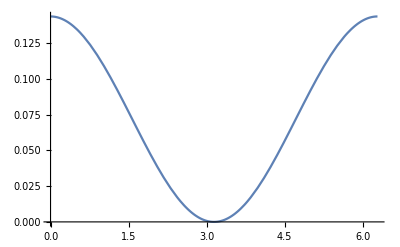

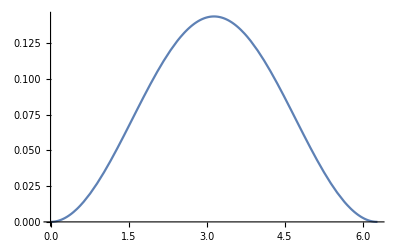

```mathematica
(* In this cell, plot the entire wave function squared at specific values of x1 and x2, as a function of sigma1 and sigma2. *)

x1val=r;
x2val=-r;

Clear[sigma1,sigma2];

psitotal[sigma1_,sigma2_]:=-psipm[x1val,x2val]*Exp[I*sigma1]-
psipm[x2val,x1val]*Exp[I*sigma2]+
(1+Exp[I*(sigma1+sigma2)])*psi[x1val,x2val];

probtotal[sigma1_,sigma2_]=Re[Conjugate[psitotal[sigma1,sigma2]]*psitotal[sigma1,sigma2]];

Plot[probtotal[0,sigma2],{sigma2,0,2*Pi}]
Plot[probtotal[Pi,sigma2],{sigma2,0,2*Pi}]
```

```mathematica
(* In this cell, calculate the wave function just after the beam splitter using Saurabh's choice of phase. *)
(* This is equivalent to reversing the sign or r. *)


(* Calculate the wave function. *)

psi[x1_,x2_]:=NIntegrate[Exp[-I*n*phi]*Exp[I*r/Sqrt[2]*Sin[phi]*x1]*Exp[-I*r/Sqrt[2]*Sin[phi]*x2]*Exp[-(x1-r/Sqrt[2]*Cos[phi])^2/(2*w^2)]*Exp[-(x2+r/Sqrt[2]*Cos[phi])^2/(2*w^2)],{phi,0,2*Pi}];

(* Calculate the probability density. *)
prob[x1_,x2_] := Re[Conjugate[psi[x1,x2] ]*psi[x1,x2] ];

(* Plot the probability density. *)
limits = 8.0;

Print[" "];Print[" "];
Print["Plot of phi++ squared, same as phi-- and after beam splitter: "];

optionplot=1;
If[optionplot==1,Plot3D[prob[x1,x2],{x1,-limits,limits},{x2,-limits,limits},PlotRange->All,PlotPoints->25]  ]
```

Plot of phi++ squared, same as phi-- and after beam splitter:

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in phi near {phi} = {4.79213}. NIntegrate obtained 1.09231×10^-17+1.78361×10^-23 ⅈ and 3.38762×10^-22 for the integral and error estimates.

-Graphics3D-